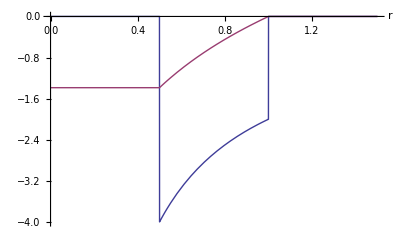

```mathematica
Needs["PlotLegends`"];
(* Radial potential and field *)
g1 =Plot[{Piecewise[{{0,r<0.5},{-2/r,r>0.5 && r < 1}}],Piecewise[{{-2Log[2],r<0.5},{2Log[r],r>0.5 && r < 1}}]},{r,0,1.5},Exclusions->None,AxesLabel->Automatic,PlotRangePadding->.1,PlotLegend->{"E_r","ψ"},LegendShadow->None,LegendSize->{0.4,0.3},LegendPosition->{0.4,-0.5}]
```

```mathematica
Export["/Users/sgess/Desktop/FACET/hollow_chan/figures/fields.pdf",g1,ImageResolution->600];
```

```mathematica
(*s=NDSolve[{(2+2Log[r[ξ]])r''[ξ]+(r'[ξ])^2/r[ξ] == 0,r[0]==1,r'[0]==-0.46191},r,{ξ,0,1}]*)
s=NDSolve[{(2+2Log[r[ξ]])r[ξ]*r''[ξ]+(r'[ξ])^2 == 0,r[0]==1,r'[0]==-0.4},r,{ξ,0,1}]
```

{{r→InterpolatingFunction[{{0.,1.}},<>]}}

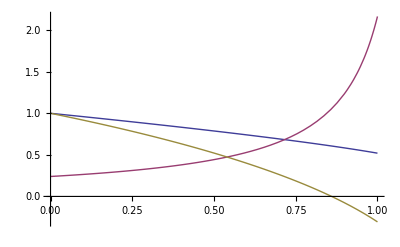

```mathematica
Needs["PlotLegends`"];(*g2=Plot[{Evaluate[r[ξ]/.s],Evaluate[2r'[ξ]/r[ξ]/.s]},{ξ,0,1},AxesLabel->Automatic,PlotLegend->{"r_s","E_z"},LegendShadow->None,LegendSize->{0.4,0.3},LegendPosition->{-0.8,-0.6}]*)
Plot[{Evaluate[r[ξ]/.s],Evaluate[-(r''[ξ]-(r'[ξ])^2/r[ξ])/.s],Evaluate[1+2Log[r[ξ]]/.s]},{ξ,0,1}]
```

```mathematica
Export["/Users/sgess/Desktop/FACET/hollow_chan/figures/sheath.pdf",g2,ImageResolution->600];
```

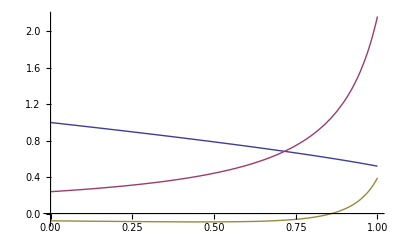

```mathematica
Plot[{Evaluate[r[ξ]/.s],Evaluate[-(r''[ξ]-(r'[ξ])^2/r[ξ])/.s],Evaluate[-(r''[ξ]+(r'[ξ])^2/r[ξ])/.s]},{ξ,0,1}]
```

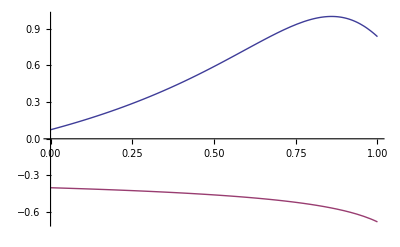

```mathematica
Plot[{Evaluate[1-2(1+2Log[r[ξ]])^2/(1+(1+r'[ξ]^2)*(1+2Log[r[ξ]])^2)/.s],Evaluate[r'[ξ]/.s]},{ξ,0,1}]
```

```mathematica
xi =0.9;
```

```mathematica
rs = r[xi]/.s[[1]]
```

0.58328

```mathematica
rin = 1/r[xi]^2*(r''[xi]*r[xi]-(r'[xi])^2)/.s[[1]]
rout = (r''[xi]*r[xi]+(r'[xi])^2)/.s[[1]]
```

-2.12723

-0.029441

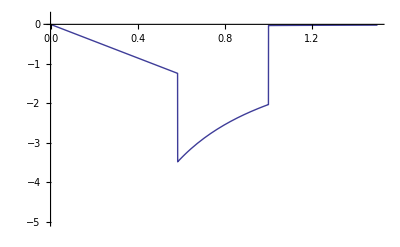

```mathematica
Plot[Piecewise[{{R*rin,R<rs},{-2/R +1/R*rout,R>rs &&R<1 },{1/R*rout,R>1}}],{R,0,1.5},PlotRange->{{0,1.5},{-5,0.2}},Exclusions->None]
```

```mathematica
λ=-0.1;
t=NDSolve[{(1-λ-λ*2Log[r[ξ]])r[ξ]*r''[ξ]-λ*(r'[ξ])^2 == 0,r[0]==.99,r'[0]==-0.01},r,{ξ,0,88}];
```

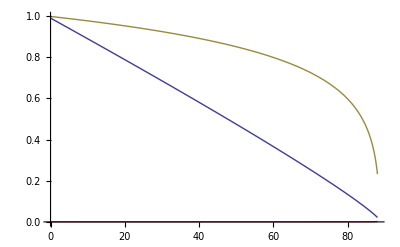

```mathematica
Plot[{Evaluate[r[ξ]/.t],Evaluate[λ*(r''[ξ]-(r'[ξ])^2/r[ξ])/.t],Evaluate[1-2*λ*Log[r[ξ]]/.t]},{ξ,0,88}]
```

```mathematica
u=NDSolve[{(2+2Log[r[ξ]])r[ξ]*r''[ξ]+3*(r'[ξ])^2 -2== 0,r[0]==1,r'[0]==-0.815},r,{ξ,0,10}]
```

{{r→InterpolatingFunction[{{0.,10.}},<>]}}

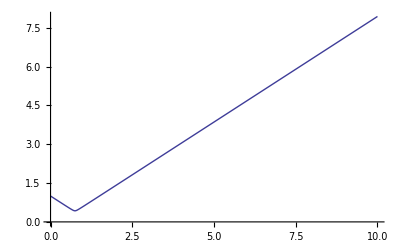

```mathematica
Plot[Evaluate[r[ξ]/.u],{ξ,0,10}]
```